```mathematica
extractViews[ll_]:=Flatten[Union[Extract[ll,Position[ll,#]]&/@{ViewPoint->_,ViewCenter->_,ViewVertical->_,ViewAngle->_,ViewVector->_,ViewRange->_}]];
```

```mathematica
wave[x_,y_,t_,x0_,y0_] := Cos[k Sqrt[(x-x0)^2 +(y-y0)^2] - ω t]/(√(x^2+y^2))
s=1;
k=3;ω=1;
xmax = 20;
ymax = 30;
ymax=30;
ymin = -30;
d=10;
Manipulate[
Show[
Plot3D[wave[x,y,t,-d/2,0]+wave[x,y,t,d/2,0],{x,-xmax,xmax},{y,1,ymax},MaxRecursion->9,PlotPoints->20,PlotRange->{{-xmax,xmax},{ymin,ymax},{-2,2}},Mesh->None,PlotStyle->Directive[Blue,Specularity[White,20],Opacity[1]],BoxRatios->{2 xmax, ymax,10},ViewPoint->Top, ViewAngle->Pi/7,Boxed->False,Axes->False],
Plot3D[Cos[k y-ω t]/(d/2),{x,-xmax,xmax},{y,ymin,1},MaxRecursion->9,PlotPoints->20,Mesh->None,PlotStyle->Directive[Blue,Specularity[White,20],Opacity[1]]]
,
Graphics3D[Cuboid[{-xmax,0,-2},{-d/2-s,1,2}]],
Graphics3D[Cuboid[{d/2+s,0,-2},{xmax,1,2}]],
Graphics3D[Cuboid[{-d/2,0,-2},{d/2,1,2}]]
]
,{t,0,2 Pi/ω}]
```

```mathematica
Show[
Plot3D[wave[x,y,0,-d/2,0]+wave[x,y,0,d/2,0],{x,-xmax,xmax},{y,1,ymax},MaxRecursion->9,PlotPoints->35,PlotRange->{{-xmax,xmax},{-10,ymax},{-2,2}},Mesh->None,PlotStyle->Directive[Blue,Specularity[White,20],Opacity[1]],BoxRatios->{2 xmax, ymax,10},ViewPoint->Top, ViewAngle->Pi/7,Boxed->False,Axes->False],
Plot3D[Cos[k y-ω *0]/(d/2),{x,-xmax,xmax},{y,-10,1},MaxRecursion->12,PlotPoints->35,Mesh->None,PlotStyle->Directive[Blue,Specularity[White,20],Opacity[1]]]
,
Graphics3D[Cuboid[{-xmax,0,-2},{-d/2-s,1,2}]],
Graphics3D[Cuboid[{d/2+s,0,-2},{xmax,1,2}]],
Graphics3D[Cuboid[{-d/2,0,-2},{d/2,1,2}]]
]
```

-Graphics3D-

```mathematica
view=extractViews[-Graphics3D-]
```

{ViewAngle→π/7,ViewPoint→{5.00783×10^-6,-0.100441,1.99748},ViewVertical→{0.0000497956,-0.998738,-0.0502204}}

```mathematica
Manipulate[Plot[wave[x,ymax,t,-d/2,0]+wave[x,ymax,t,d/2,0],{x,-xmax,xmax},PlotRange->{-0.1,0.1}],{t,0,2 Pi/ω}]
```

```mathematica
Manipulate[Plot[(wave[x,ymax,t,-d/2,0]+wave[x,ymax,t,d/2,0])^2,{x,-xmax,xmax},PlotRange->{-0.01,0.01}],{t,0,2 Pi/ω}]
```

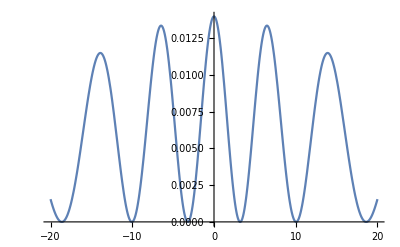

```mathematica
Plot[NIntegrate[(wave[x,ymax,t,-d/2,0]+wave[x,ymax,t,d/2,0])^2,{t,0,2 Pi/ω}],{x,-xmax,xmax}]
```

```mathematica
anim=Table[
Show[
Plot3D[wave[x,y,t,-d/2,0]+wave[x,y,t,d/2,0],{x,-xmax,xmax},{y,1,ymax},MaxRecursion->15,PlotPoints->100,PlotRange->{{-xmax,xmax},{ymin,ymax},{-2,2}},Mesh->None,PlotStyle->Directive[Blue,Specularity[White,20],Opacity[1]],BoxRatios->{2 xmax, ymax,10},Boxed->False,Axes->False,ImageSize->Large,
ViewAngle->π/7,ViewPoint->{5.007827549165246*^-6,-0.1004408235443196,1.9974763179924169},ViewVertical->{0.00004979557399433266,-0.9987381577548572,-0.050220411834581216}
],
Plot3D[Cos[k y-ω t],{x,-xmax,xmax},{y,ymin,1},MaxRecursion->15,PlotPoints->40,Mesh->None,PlotStyle->Directive[Blue,Specularity[White,20],Opacity[1]]]
,
Graphics3D[Cuboid[{-xmax,0,-2},{-d/2-s,1,2}]],
Graphics3D[Cuboid[{d/2+s,0,-2},{xmax,1,2}]](*,
Graphics3D[Cuboid[{-d/2,0,-2},{d/2,1,2}]]*)
]
,{t,0,2 Pi/ω,2 Pi/ω/40}];
```

```mathematica
Export["singleslid3.gif",anim]
```

C:\Users\rafae\Desktop\Anne\singleslid3.gif

```mathematica
rmax = 50;
r0 = 0;
dr = 1.5;
d=8;
s=1;
xmax = 20;
ymax = 30;
Animate[
Show[
Graphics[Table[Circle[{-d/2,0},r],{r,r0,rmax,dr}]~Join~Table[Circle[{d/2,0},r],{r,r0,rmax,dr}],PlotRange->{{-xmax-d/2, xmax+d/2}, {0, ymax}}],
Graphics[{
{Thickness[0.03],Line[{{-rmax*2,0},{-d/2-s,0}}]},
{Thickness[0.03],Line[{{d/2+s,0},{rmax*2,0}}]},
{Thickness[0.03],Line[{{-d/2+s,0},{d/2-s,0}}]}
}
]
]
,{r0,0,dr}]
```